# Chapter 3 : Special Functions

## Hypergeometric ODE (Chapter 18.5)

The defining ODE
The hypergeometric equation is defined in the textbook as
x(x-1)y'' + [(1+a+b)x + c]y' + a b y = 0
NOTE: The Mathematica convention is slightly different from the textbook (they use c → -c):
x(x-1)y'' + [(1+a+b)x - c]y' + a b y = 0

Singularities
It has regular singularities at 0,1,∞.

Solutions
The hypergeometric function is typically written as
_2 F_1(a,b,c;z)=∑_(n=0)^∞ ((a)_n(b)_n)/((c)_n)z^n/(n!)  (with c ϵ ℕ )
Here, (q)_n is the so-called (ascending) Pochhammer symbol:
 (q)_n=Piecewise[{{1, n=0}, {q(q+1)...(q+n), n>0}}]
The Hypergeometric Function is implemented in Mathematica via Hypergeometric2F1.

Properties
If a or b are non-positive integers, the series terminates and the hypergeometric function is just a polynomial. There are hundreds of identities for hypergeometric functions. Moreover, they are related to many elementary functions, such as the logarithm (see below).

Appearance
It is ubiquitous since any ODE with 3 regular points can be brought into this form by a change of variables.
As many linear second-order ODEs it is closely related to the wave equation and hence it appears as solutions to Quantum Mechanics systems and in Electromagnetism. Beyond that, it appears in Statistical Mechanics (random walks, probability distributions), Field Theory (correlation functions) and Mathematical Physics (string theory).

Definition

```mathematica
Series[Hypergeometric2F1[a,b,c,x],{x,0,3}]//Normal
```

1+(a b x)/c+(a (1+a) b (1+b) x^2)/(2 c (1+c))+(a (1+a) (2+a) b (1+b) (2+b) x^3)/(6 c (1+c) (2+c))

Solution of the Hypergeometric Differential Equation

```mathematica
y[x_]:=Hypergeometric2F1[a,b,c,x]
x(x-1)y''[x]+((1+a+b)x-c)y'[x]+ a b y[x]==0//FullSimplify
```

True

Behavior at 0

```mathematica
Series[Hypergeometric2F1[2, 3, 4, x], {x, 0, 3}] //Normal// FullSimplify
Limit[Hypergeometric2F1[2, 3, 4, x],{x->0}]
```

1+(3 x)/2+(9 x^2)/5+2 x^3

1

Behavior at 1

```mathematica
Series[Hypergeometric2F1[2, 3, 4, x], {x, 1, 3}] //Normal// FullSimplify
Limit[Hypergeometric2F1[2, 3, 4, x],{x->1}]
```

(-75+3 x (70+x (-80+(43-9 x) x))-6 (-1+x) (-20+x (45+2 x (-18+5 x))) Log[1-x])/(-1+x)

Indeterminate

Behavior at ∞

```mathematica
Series[Hypergeometric2F1[2,3,4,x],{x,∞,5}]//Normal
Limit[Hypergeometric2F1[2, 3, 4, x],{x->∞}]
```

-6/x^5-9/x^4+3/x^2+(3 (-1+2 Log[-x]))/x^3

0

Special behavior

```mathematica
Grid[Table[{a,Hypergeometric2F1[-a,3,4,x]},{a,0,5}],Frame->All]//FullSimplify
```

0 | 1
1 | 1-(3 x)/4
2 | 1+3/10 x (-5+2 x)
3 | 1-1/20 x (45+2 x (-18+5 x))
4 | 1-3 x+(18 x^2)/5-2 x^3+(3 x^4)/7
5 | 1-(15 x)/4+6 x^2-5 x^3+(15 x^4)/7-(3 x^5)/8

```mathematica
Hypergeometric2F1[1,1,2,-x]//FullSimplify
```

Log[1+x]/x

Plots of the function

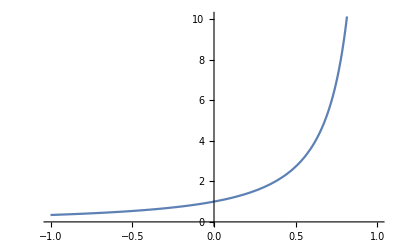

```mathematica
Plot[Hypergeometric2F1[2,3,4,x],{x,-1,1}]
```

```mathematica
ComplexPlot3D[Hypergeometric2F1[2,3,4,z],{z,-2-2I,2+2I},PlotLegends->Automatic]
```

-Graphics3D-

## Legendre ODE (Chapter 15)

The defining ODE
The Legendre equation is 
(1-x^2)y'' -2 x y' + l (l + 1) y = 0

Singularities
It has regular singularities at -1,1,∞.

Solutions
The Legendre ODE also has 3 regular singularities and can hence be expressed in terms of the hypergeometric function. 
In more detail:
For |1-z| < 2:    P(l,x) = _2 F_1(-l,l+1,1;(1-z)/2)
For     |z| > 1:   Q(l,x) = (√π)/2^(l+1) (Γ(l+1))/(Γ(l+3/2))1/z^(l+1) _2 F_1((l+1)/2,(l+2)/2,(2l+3)/2;1/z^2)
For integer l, P and Q are called the Legendre functions of the first and second kind, respectively. They are implemented in Mathematica via LegendreP and LegendreQ.

Properties
In their general form, they inherit the properties of the hypergeometric function. Their generating function has a physical interpretation, see below under Appearance.
If l is a non-negative integer and |x|<=1, P(l,x) is polynomial. The corresponding polynomials are the so-called Legendre Polynomials. The Legendre polynomials are orthogonal with respect to an inner product
(2 n + 1)/2 ∫_-1^1 P(m,x) P(n,x)ⅆx = δ_(m,n)

Since the argument of the polynomial is in the interval [-1,1], which is the range of the trigonometric functions sin(θ) and cos(θ), one often finds them to depend on a variable through these functions, P(n, cos(θ)). The Legendre polynomials also form a complete orthogonal basis, i.e., any (piecewise continuous) function (with finitely many discontinuities) in the interval [-1,1] can be represented by a series expansion of Legendre polynomials:
f(x) = ∑_(l=0)^∞ a_l P(l,x)      where       a_l = (2 l + 1)/2 ∫_-1^1 f(x)P(l,x)ⅆx

Appearance
Legendre functions appear as a special case of hypergeometric functions in wave problems with spherical symmetries (so-called central force problems, which only depend on the radial distance from the center). These include 
- in gravity: gravitational fields of the Earth or other spherical objects
- in E&M:      electrostatic potentials for a ring of charge, electric multipoles, circular current loops, etc.
In particular, the potential induced by a point charge q at a point z_* on the positive z-axis at some point  (r,θ,ϕ) in spherical coordinates (since the charge is along the z-axis, the potential is actually the same of all ϕ, i.e., it does not depend on ϕ) can be written as
V(r,θ)=q/(4π ϵ_0 r) ∑_(n=0)^∞ P(n,cos(θ))(a/r)^n
Turning this around, the generating function for the Legendre polynomial has a physical interpretation: the n^th Legendre polynomial gives the angular dependence of the  (a/r)^n term of the potential. The generating function can be written as
 ∑_(n=0)^∞ P(n,x) t^n =1/(√(1-2x t+t^2)) 
By comparing both sides, we can read off the n^th Legendre polynomial as the coefficient in front of the t^nterm of the series expansion of the expression on the right.

### General Function

Definition

```mathematica
Series[LegendreP[l,x],{x,0,3}]//Normal//FullSimplify
```

1/3 √π ((6-3 l (1+l) x^2)/(l Gamma[1/2-l/2] Gamma[l/2])+(-6 x+(-2+l+l^2) x^3)/(Gamma[-l/2] Gamma[(1+l)/2]))

Solution of the Legendre Differential Equation

```mathematica
y[x_]:=LegendreP[l,x]
(1-x^2)y''[x]-2x y'[x]+l(l+1)y[x]==0//FullSimplify
```

True

Behavior at -1

```mathematica
Series[LegendreP[1/2, x], {x, 0, 3}] //Normal// FullSimplify
Limit[LegendreP[1/2, x],{x->-1}]
```

(2 (8-3 x^2) Gamma[-1/4]^2+(7 √2 π x (24+5 x^2) Gamma[5/4])/Gamma[11/4])/(128 π^(3/2))

-∞

Behavior at 1

```mathematica
Series[LegendreP[1/2, x], {x, 0, 3}] //Normal// FullSimplify
Limit[LegendreP[1/2, x],{x->1}]
```

(2 (8-3 x^2) Gamma[-1/4]^2+(7 √2 π x (24+5 x^2) Gamma[5/4])/Gamma[11/4])/(128 π^(3/2))

1

Behavior at ∞

```mathematica
Series[LegendreP[1/2, x],{x,∞,5}]//Normal//FullSimplify
Limit[LegendreP[1/2, x],{x->∞}]
```

(-109+180 Log[2]+64 x^2 (-3+16 x^2+Log[64])+4 (15+32 x^2) Log[x])/(256 √2 π x^(7/2))

∞

Plots of the function

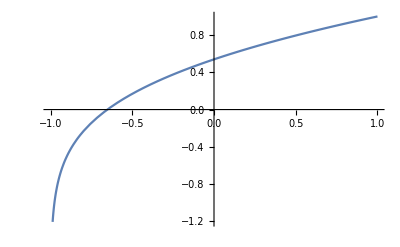

```mathematica
Plot[LegendreP[1/2, x],{x,-1,1}]
```

```mathematica
ComplexPlot3D[LegendreP[1/2, z],{z,-2-2I,2+2I},PlotLegends->Automatic]
```

-Graphics3D-

### Legendre Polynomials

For l ϵ ℤ_(>=0), the solutions are the so-called Legendre Polynomials. Note that they are even (for even n) or odd (for odd n)

```mathematica
Table[{l,LegendreP[l,x]},{l,0,5}]//Grid//Expand
```

0 | 1
1 | x
2 | 1/2 (-1+3 x^2)
3 | 1/2 (-3 x+5 x^3)
4 | 1/8 (3-30 x^2+35 x^4)
5 | 1/8 (15 x-70 x^3+63 x^5)

```mathematica
polys=Table[LegendreP[l,x],{l,0,5}];
```

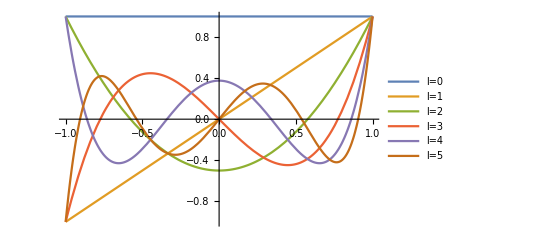

```mathematica
Plot[polys,{x,-1,1},PlotLegends->Table["l="<>ToString[l],{l,0,5}]]
```

We can compare this with the generating function

```mathematica
CoefficientList[Series[1/Sqrt[1-2x t+t^2],{t,0,6}]//Normal, t]//FullSimplify//MatrixForm
```

(1
x
1/2 (-1+3 x^2)
1/2 x (-3+5 x^2)
1/8 (3-30 x^2+35 x^4)
1/8 x (15-70 x^2+63 x^4)
1/16 (-5+21 x^2 (5-15 x^2+11 x^4)))

The Legendre Polynomials are orthogonal with respect to the following inner product

```mathematica
Table[(2n+1)/2 Integrate[LegendreP[m,x] LegendreP[n,x],{x,-1,1}],{m,0,5},{n,0,5}]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

They are also complete, i.e., they can approximate any function (under mild assumptions, see above)

```mathematica
f[x_]:=Exp[x];
fApprox[x_,n_]:=Module[{LegendrePolys,l,as},(
LegendrePolys=Table[LegendreP[l,z],{l,0,n}];
as=ParallelTable[(l-1/2) Integrate[f[z]LegendrePolys[[l]],{z,-1,1}],{l,1,n+1}];
Return[Sum[as[[i]] LegendrePolys[[i]],{i,Length[as]}]/.{z->x}];
)];
approxs=Table[fApprox[x,n],{n,{0,1,5,10}}];
approxErrors=Table[Abs[fApprox[x,n]-Exp[x]],{n,{0,1,5,10}}];
AppendTo[approxs,Exp[x]];
```

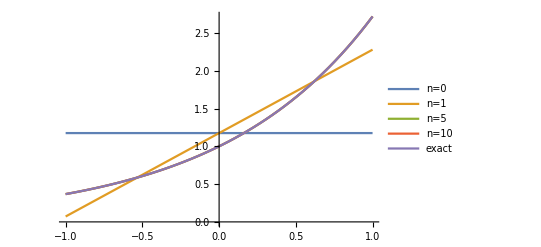

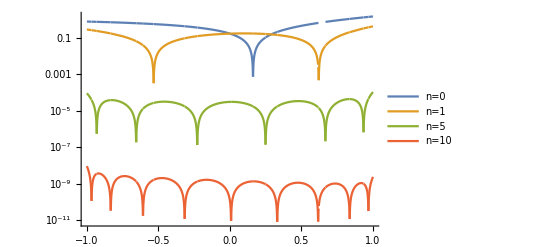

```mathematica
Plot[approxs,{x,-1,1},PlotLegends->Join[Table["n="<>ToString[n],{n,{0,1,5,10}}],{"exact"}]]
LogPlot[Evaluate[approxErrors],{x,-1,1},PlotLegends->Table["n="<>ToString[n],{n,{0,1,5,10}}]]
```

## Chebyshev ODE (Chapter 18.4)

The defining ODE
The Chebyshev equation is 
(1-x^2)y'' - x y' + n^2 y = 0

Singularities
It has regular singularities at -1,1,∞.

Solutions
The Legendre ODE also has 3 regular singularities and can hence be expressed in terms of the hypergeometric function. The coefficients of the power series of the solution T(n,x)=∑_(p=0)^∞ a_p(n)x^p satisfy the recursion relation
a_(p+2)=((p - n) (p + n))/((p + 1) (p + 2)))a_p
which converges for |x| < 1. Note that this is a whole family of solutions with a_0 and a_1 undetermined. A common choice is a_0= a_1=1.

Properties
They inherit the properties of the hypergeometric function. If n is an integer and |x| < 1, T(n,x) is polynomial. The corresponding polynomials are the so-called Chebyshev Polynomials. The generating function for the Chebyshev polynomials is a generalization of the one for the Legendre Polynomials:
 ∑_(n=0)^∞ C(n,α,x) t^n =1/((1-2x t+t^2)^α) 
This reproduces the Legendre polynomials for α = 1/2. The Chebyshev polynomial T(n,x) corresponds to α → 0. This definition requires some care in taking this limit. In that limit, the generating function can be written as
T(n,x) + 2 ∑_(n=1)^∞ T(n,x) t^n =(1-t^2)/(1-2x t+t^2)    with  T(0,x)=1  
Albeit unintuitive, they can also be written as
T(n,x)=Piecewise[{{cos(n arccos(x))
cosh(n arccosh(x)), if |x|< 1
        if  x ≥ 1}, {(-1)^n cosh(n arcosh(-x)), if x ≤ -1}}]
Remarkably, the expressions on the RHS are polynomial.

Another common choice for α is α=1, which is sometimes called the Chebyshev polynomials of the second kind. They are typically denoted by U(n,x) and their generating polynomial is simply
 ∑_(n=0)^∞ C(n,1,x) t^n = ∑_(n=0)^∞ U(n,x) t^n =1/(1-2x t+t^2) 
Like the Legendre Polynomials, the Chebyshev polynomials also form a complete orthogonal polynomial basis (with respect to a slightly different inner product). Their orthogonality relation is
2/π ∫_-1^1 T(m,x) T(n,x)1/(√(1-x^2))ⅆx = δ_(m,n)    for m,n ≠0,0 (for m=n=0, the integral is 2)
2/π ∫_-1^1 U(m,x) U(n,x)1/(√(1-x^2))ⅆx = δ_(m,n) 

Appearance
Chebyshev functions also appear as a special case of hypergeometric functions in wave problems. They also appear in signal processing (Chebyshev filters) and in Chaos Theory.
Finally, they play an important role in polynomial interpolation, where they have the property that if the interpolation points are taken to be the zeros of the polynomial, they minimize the maximum error:
Let P_(n-1)(x) be the unique polynomial of degree (at most) n-1 that interpolates n points {x_1,... , x_n}. The error between this interpolating polynomial and the actual function f(x) is then
Err_n=|f(x)-P_(n-1)(x)|=(f^(n)(ξ))/(n!)(x-x_1)...(x-x_n) ≤ (x-x_1)...(x-x_n) max_(y ϵ [-1,1])|f^(n)(y)|     with ξ ϵ [-1, 1]
We used the same estimate for the remainder when showing that Newton’s method is a second order method. The part max_(y ϵ [-1,1]) |f^(n)(y)| is fixed by the function we want to interpolate and we have no control over it. We might, however, have control over the points x_i. If so, this begs the question which x_i we should choose to minimize (x-x_1)...(x-x_n). One can show that (x-x_1)...(x-x_n)≥2^(1-n). The lower bound is saturated if the x_i are chosen to be the zeros of the n^th Chebyshev polynomial. These are also called Chebyshev nodes.

### General Function

Definition

```mathematica
Series[ChebyshevT[n,x],{x,0,3}]//Normal//FullSimplify
Series[ChebyshevU[n,x],{x,0,3}]//Normal//FullSimplify
```

(1-(n^2 x^2)/2) Cos[(n π)/2]+1/6 n x (6-(-1+n^2) x^2) Sin[(n π)/2]

-1/2 (-2+n (2+n) x^2) Cos[(n π)/2]-1/6 (1+n) x (-6+(-1+n) (3+n) x^2) Sin[(n π)/2]

Solution of the Legendre Differential Equation

```mathematica
y[x_]:=ChebyshevT[n,x]
(1-x^2)y''[x]-x y'[x]+n^2 y[x]==0//FullSimplify
```

True

Behavior at -1

```mathematica
Series[ChebyshevT[1/2, x], {x, 0, 3}] //Normal// FullSimplify
Limit[ChebyshevT[1/2, x],{x->-1}]
```

(16+x (8+(-2+x) x))/(16 √2)

0

Behavior at 1

```mathematica
Series[ChebyshevT[1/2, x], {x, 0, 3}] //Normal// FullSimplify
Limit[ChebyshevT[1/2, x],{x->1}]
```

(16+x (8+(-2+x) x))/(16 √2)

1

Behavior at ∞

```mathematica
Series[ChebyshevT[1/2, x],{x,∞,5}]//Normal//FullSimplify
Limit[ChebyshevT[1/2, x],{x->∞}]
```

Cos[1/64 (16 π+((-x^2)^(3/2) (3+8 x^2))/x^7-(16 x Log[-4 x^2])/(√(-x^2)))]

∞

Plots of the function

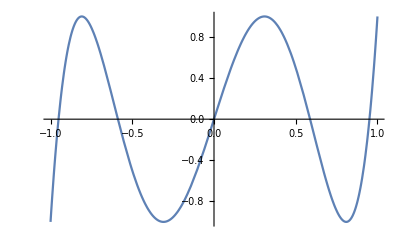

```mathematica
Plot[ChebyshevT[5, x],{x,-1,1}]
```

```mathematica
ComplexPlot3D[ChebyshevT[5, z],{z,-2-2I,2+2I},PlotLegends->Automatic]
ComplexPlot3D[ChebyshevU[5, z],{z,-2-2I,2+2I},PlotLegends->Automatic]
```

-Graphics3D-

-Graphics3D-

### Chebyshev Polynomials

For n ϵ ℤ, the solutions are the so-called Chebyshev Polynomials

```mathematica
Table[{n,ChebyshevT[n,x],ChebyshevU[n,x]},{n,0,5}]//Grid//FullSimplify
```

0 | 1 | 1
1 | x | 2 x
2 | -1+2 x^2 | -1+4 x^2
3 | -3 x+4 x^3 | -4 x+8 x^3
4 | 1-8 x^2+8 x^4 | 1-12 x^2+16 x^4
5 | 5 x-20 x^3+16 x^5 | 6 x-32 x^3+32 x^5

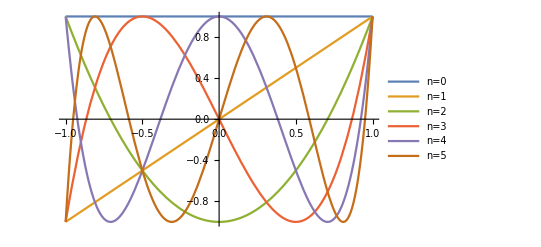

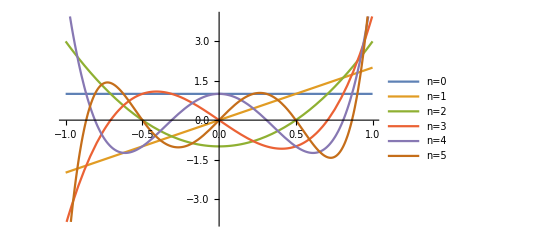

```mathematica
polysT=Table[ChebyshevT[n,x],{n,0,5}];
polysU=Table[ChebyshevU[n,x],{n,0,5}];
Plot[polysT,{x,-1,1},PlotLegends->Table["n="<>ToString[n],{n,0,5}]]
Plot[polysU,{x,-1,1},PlotLegends->Table["n="<>ToString[n],{n,0,5}]]
```

The Chebyshev Polynomials are orthogonal with respect to the following inner product

```mathematica
ParallelTable[2/π If[n==0&&m==0,1/2,1]Integrate[(ChebyshevT[m,x] ChebyshevT[n,x])/Sqrt[1-x^2],{x,-1,1}],{m,0,5},{n,0,5}]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

Let us look at polynomial interpolation of Exp[x] using random points and the Chebyshev nodes.

```mathematica
yRand=f/@xRand
```

{1.87722,0.540888,0.850758,2.12348,0.499346,1.7269,0.621288,0.902029,0.422165,1.58707}

```mathematica
f[x_]:=Exp[x];
xRand=RandomReal[{-1,1},10];
yRand=f/@xRand;
fInterRand[x_]:=ParallelSum[yRand[[i]] Product[If[j==i,1,(x-xRand[[j]])/(xRand[[i]]-xRand[[j]])],{j,Length[xRand]}],{i,Length[xRand]}];
xCheby=x/.Solve[0==ChebyshevT[10,x],x]//N;
yCheby=f/@xCheby;
fInterCheby[x_]:=ParallelSum[yCheby[[i]] Product[If[j==i,1,(x-xCheby[[j]])/(xCheby[[i]]-xCheby[[j]])],{j,Length[xCheby]}],{i,Length[xCheby]}];
```

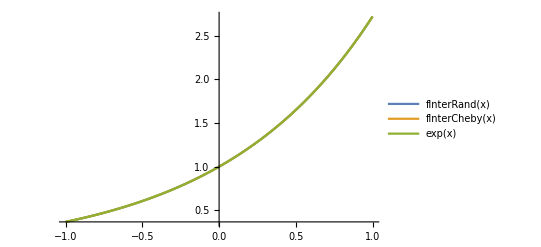

```mathematica
Plot[{fInterRand[x],fInterCheby[x],Exp[x]},{x,-1,1},PlotLegends->"Expressions"]
```

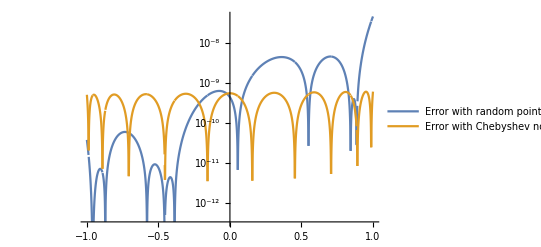

```mathematica
LogPlot[{Abs[fInterRand[x]-Exp[x]],Abs[fInterCheby[x]-Exp[x]]},{x,-1,1},PlotLegends->{"Error with random points", "Error with Chebyshev nodes"}]
```

## Confluent Hypergeometric ODE (Chapter 18.6)

The defining ODE
The confluent hypergeometric equation is
x y'' + (c-x)y' -a y = 0

Singularities
It has a regular singularity at 0 and an irregular singularity at ∞. Indeed, the confluent hypergeometric function is obtain from the general hypergeometric function by merging one of the regular finite singularities with the regular singularity at infinity. This collision of singularities worsens the singularity at infinity of the confluent hypergeometric equation to an irregular singularity.

Solutions
The confluent hypergeometric function (remember it now only depends on 2 parameters a and c) is typically written as
_1 F_1(a,c;z)=∑_(n=0)^∞ ((a)_n(b)_n)/((c)_n)z^n/(n!)  
The Confluent Hypergeometric Function is implemented in Mathematica via Hypergeometric1F1.

Properties
If a is a non-positive integers, the series terminates and the confluent hypergeometric function is just a polynomial. The function inherits identities from the hypergeometric function by specialization. Many elementary functions, such as the error function and the incomplete Gamma function, can be written in terms of confluent hypergeometric function.

Appearance
The equation also appears frequently. Other functions (that we will discuss below), such as the Bessel, Laguerre, and Hermite functions are special cases  of the confluent hypergeometric function (just like the Legendre and Chebyshev functions were special functions of the hypergeometric function).
It often appears as the solution to the radial dependence of an ODE in problems with spherical or cylindrical symmetries, e.g. gravity and astrophysics (stellar structure, gravitational collapse ), Electromagnetism, wave mechanics. It also appears in heat conduction equations, quantum mechanics, quantum field theory, etc.

Definition

```mathematica
Series[Hypergeometric1F1[a,c,x],{x,0,3}]//Normal
```

1+(a x)/c+(a (1+a) x^2)/(2 c (1+c))+(a (1+a) (2+a) x^3)/(6 c (1+c) (2+c))

Solution of the Hypergeometric Differential Equation

```mathematica
y[x_]:=Hypergeometric1F1[a,c,x]
x y''[x]+(c-x)y'[x]-a y[x]==0//FullSimplify
```

True

Behavior at 0

```mathematica
Series[Hypergeometric1F1[1,2, x], {x, 0, 3}] //Normal// FullSimplify
Limit[Hypergeometric1F1[1,2, x],{x->0}]
```

1+1/24 x (12+x (4+x))

1

Behavior at ∞

```mathematica
Series[Hypergeometric1F1[1,2, x],{x,∞,5}]//Normal
Limit[Hypergeometric1F1[1,2, x],{x->∞}]
```

-1/x+ⅇ^x/x

∞

Special behavior

```mathematica
Grid[Table[{a,Hypergeometric1F1[-a,2,x]},{a,0,5}],Frame->All]//FullSimplify
```

0 | 1
1 | 1-x/2
2 | 1+1/6 (-6+x) x
3 | 1-1/24 (-6+x)^2 x
4 | 1-2 x+x^2-x^3/6+x^4/120
5 | 1-1/720 x (1800+x (-1200+x (300+(-30+x) x)))

```mathematica
Hypergeometric1F1[1/2,3/2,-x^2]//FullSimplify
Hypergeometric1F1[a,a+1,-x]//FullSimplify
```

(√π Erf[x])/(2 x)

a x^-a Gamma[a,0,x]

Plots of the function

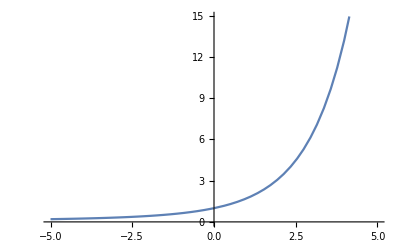

```mathematica
Plot[Hypergeometric1F1[1,2, x],{x,-5,5}]
```

```mathematica
ComplexPlot3D[Hypergeometric1F1[1,2, z^2],{z,-2-2I,2+2I},PlotLegends->Automatic]
```

-Graphics3D-

## Bessel ODE (Chapter 14.1-14.2)

The defining ODE
The Bessel equation is 
x^2 y'' + x y' +(x^2-n^2) y = 0

Singularities
It has a regular singularity at 0 and an irregular singularity at ∞ (just as the confluent hypergeometric function).

Solutions
The Bessel function (also called Bessel J function or Bessel function of the first kind) is defined as
J(n;z)=∑_(s=0)^∞ (-1)^s/(s! Γ(n+s+1))(z/2)^(n+2s)      for n!=-1,-2,-3,...     
If n is an integer Γ(n+s+1)=(n+s)! The function is available in Mathematica as BesselJ

Properties
There is also a generating series for the n^th Bessel function (for n integer) as the coefficient in front of the t^n term in the expansion,
g(z, t) = Exp[(z t)/2 - x/(2 t)]     
The Bessel function also satisfies a recurrence relation
J(n-1,z) +J(n+1,z) = (2n)/z J(n,z)
J(n-1,z) -J(n+1,z) = 2 J'(n,z)
In the second equation, J'(n,z) denotes the derivative with respect to z. In fact, one can show that any function that satisfies these recurrence relations also satisfies the defining ODE given above.
The (integral) Bessel functions also satisfy an orthogonality condition with respect to an inner product. The condition involves the zeros α_(n,i) of the Bessel function, where n is the integer in the defining ODE and i labels the different zeros. The zeros of the Bessel function appear frequently, and Mathematica has a built-in function called BesselJZero to compute them. In general, there is no analytic expression for them and one has to find them numerically. Also, the Bessel functions are oscillatory, so there are in general infinitely many zeros. Finally, they are even or odd functions for even or odd n, so the zeros come in pairs α_(n,i)=α_(-n,i). This is also evident from the defining equation, which only depends on n^2.
The orthogonality condition reads
∫_0^a x J(n,α_(n,i)x/a)J(n,α_(n,j)x/a)ⅆx = δ_(i,j) ((1/2)[a J(n + 1, α_(n,i))])^2

Appearance
The equation appears ubiquitously, also mostly in problems with cylindrical or spherical symmetry (since they are specializations of the confluent hypergeometric functions), when the problem separates into functions that only depend on the cylindrical coordinates (ρ,ϕ,z) or  the spherical coordinates (r,θ,ϕ) separately. They also play a role in Diffraction and Scattering processes.

There are many related functions such as the Bessel Functions of the second kind (aka Neumann Functions), the Bessel Functions of the third kind (aka Hankel Functions), generalized Bessel Functions, Spherical Bessel Functions, generalized Spherical Bessel Functions,... They satisfy similar equations as the Bessel Functions of the first kind. You can read up on them in the rest of Chapter 14 of the book should you ever need them (I haven’t, and I have never met a person who needed them beyond solving some textbook homework problem). They are all available in Mathematica as BesselI, BesselJ, BesseIK, BesselY.

Definition

```mathematica
Series[BesselJ[n,x],{x,0,3}]//Normal
```

x^n (2^-n/Gamma[1+n]-(2^(-2-n) x^2)/((1+n) Gamma[1+n]))

Solution of the Hypergeometric Differential Equation

```mathematica
y[x_]:=BesselJ[n,x]
x^2 y''[x]+x y'[x]+(x^2-n^2) y[x]==0//FullSimplify
```

True

Behavior at 0

```mathematica
Series[BesselJ[1,x], {x, 0, 3}] //Normal// FullSimplify
Limit[BesselJ[1,x],{x->0}]
```

-1/16 x (-8+x^2)

0

Behavior at ∞

```mathematica
Series[BesselJ[1,x],{x,∞,5}]//Normal// FullSimplify
Limit[BesselJ[1,x],{x->∞}]
```

((4725-256 x^2 (15+128 x^2)) Cos[π/4+x]+96 x (-35+128 x^2) Sin[π/4+x])/(16384 √(2 π) x^(9/2))

0

Plots of the function

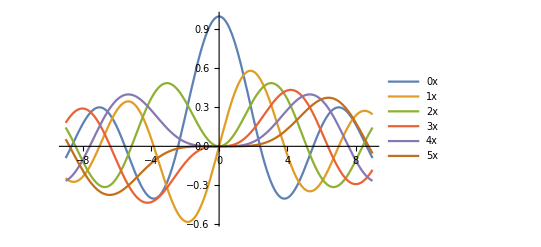

```mathematica
Plot[Evaluate[Table[BesselJ[n, x],{n,0,5}]],{x,-9,9},PlotLegends->"Expressions"]
```

```mathematica
ComplexPlot3D[BesselJ[1/2, z],{z,-2-2I,2+2I},PlotLegends->Automatic]
```

-Graphics3D-

Recurrence Relation

```mathematica
BesselJ[n-1,x]+BesselJ[n+1,x]//FullSimplify
BesselJ[n-1,x]-BesselJ[n+1,x]//FullSimplify
```

(2 n BesselJ[n,x])/x

BesselJ[-1+n,x]-BesselJ[1+n,x]

The second Identity is not applied automatically by Mathematica' s simplify function . Let us check it manually:

```mathematica
BesselJ[n-1,x]-BesselJ[n+1,x]-2D[BesselJ[n,x],x]
```

0

Roots and Orthogonality

```mathematica
FindRoot[BesselJ[1,x]==0,{x,0}]
FindRoot[BesselJ[1,x]==0,{x,2}]
FindRoot[BesselJ[1,x]==0,{x,4}]
FindRoot[BesselJ[1,x]==0,{x,6}]
```

{x→0.}

{x→10.1735}

{x→3.83171}

{x→7.01559}

```mathematica
Table[BesselJZero[1,i],{i,10}]//N
```

{3.83171,7.01559,10.1735,13.3237,16.4706,19.6159,22.7601,25.9037,29.0468,32.1897}

```mathematica
ParallelTable[Integrate[x BesselJ[1,BesselJZero[1,i] x/a] BesselJ[1,BesselJZero[1,j] x/a],{x,0,a}],{i,5},{j,5}]//FullSimplify//MatrixForm
```

(-1/2 a^2 BesselJ[0,BesselJZero[1,1]] BesselJ[2,BesselJZero[1,1]] | 0 | 0 | 0 | 0
0 | -1/2 a^2 BesselJ[0,BesselJZero[1,2]] BesselJ[2,BesselJZero[1,2]] | 0 | 0 | 0
0 | 0 | -1/2 a^2 BesselJ[0,BesselJZero[1,3]] BesselJ[2,BesselJZero[1,3]] | 0 | 0
0 | 0 | 0 | -1/2 a^2 BesselJ[0,BesselJZero[1,4]] BesselJ[2,BesselJZero[1,4]] | 0
0 | 0 | 0 | 0 | -1/2 a^2 BesselJ[0,BesselJZero[1,5]] BesselJ[2,BesselJZero[1,5]])

## Laguerre ODE (Chapter 18.3)

The defining ODE
The Laguerre equation is 
x y'' + (1-x) y' +a y = 0

Singularities
It has a regular singularity at 0 and an irregular singularity at ∞ (just as the confluent hypergeometric function).

Solutions
One typically only uses the Laguerre polynomials, which appear if a  is a non-negative integer. The function is available in Mathematica as LaguerreL

Properties
There is also a generating series for the a^th Laguerre function (for a integer) as the coefficient in front of the t^a term in the expansion,
g(z, t) = 1/(1-t)Exp[-(x t)/(1-t)]     
Note that this generating function implies that L(n;0)=1 for all n.

The Laguerre function also satisfies  recurrence relations
(a+1) L(a+1, z) = (2a+1-x) L(a, z) -a L(a-1, z)
x L'(a+1, z) = n (L(a, z) - L(a-1, z))
Here, L'(a,z) denotes the derivative with respect to z.
The Laguerre polynomials also satisfy an orthogonality condition with respect to an inner product:
∫_0^a ⅇ^-x L(a,x)L(b,x)ⅆx = δ_(a,b)

Appearance
The equation appears ubiquitously, also mostly in problems with cylindrical or spherical symmetry (since they are specializations of the confluent hypergeometric functions), when the problem separates into functions that only depend on the cylindrical coordinates (ρ,ϕ,z) or  the spherical coordinates (r,θ,ϕ) separately. They also play a role in Diffraction and Scattering processes. They are perhaps best-known for their appearance in the solution to the radial part of the wave function for the electron in the Hydrogen atom.

Definition

```mathematica
Series[LaguerreL[a,x],{x,0,5}]//Normal
```

LaguerreL[a,0]-1/120 x^5 LaguerreL[-5+a,5,0]+1/24 x^4 LaguerreL[-4+a,4,0]-1/6 x^3 LaguerreL[-3+a,3,0]+1/2 x^2 LaguerreL[-2+a,2,0]-x LaguerreL[-1+a,1,0]

Solution of the Laguerre Differential Equation

```mathematica
y[x_]:=LaguerreL[a,x]
x y''[x]+(1-x) y'[x]+a y[x]==0//FullSimplify
```

True

Behavior at 0

```mathematica
Series[LaguerreL[1,x], {x, 0, 3}] //Normal// FullSimplify
Limit[LaguerreL[1,x],{x->0}]
```

1-x

1

Behavior at ∞

```mathematica
Series[LaguerreL[1,x],{x,∞,5}]//Normal// FullSimplify
Limit[LaguerreL[1,x],{x->∞}]
```

1-x

-∞

Plots of the function

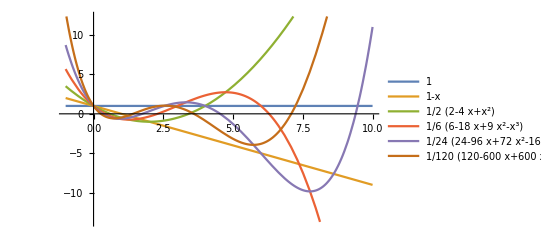

```mathematica
Plot[Evaluate[Table[LaguerreL[n, x],{n,0,5}]],{x,-1,10},PlotLegends->"Expressions"]
```

```mathematica
ComplexPlot3D[LaguerreL[1/2, z],{z,-2-2I,2+2I},PlotLegends->Automatic]
```

-Graphics3D-

Laguerre Polynomials

```mathematica
Grid[Table[{a,LaguerreL[a,x]},{a,0,5}],Frame->All]//FullSimplify
```

0 | 1
1 | 1-x
2 | 1+1/2 (-4+x) x
3 | 1-1/6 (-6+x) (-3+x) x
4 | 1+1/24 (-4+x) x (24+(-12+x) x)
5 | 1-1/120 x (30+(-15+x) x) (20+(-10+x) x)

Recurrence Relation

```mathematica
(2a+1-x)LaguerreL[a,x]-a LaguerreL[a-1,x]//FullSimplify
LaguerreL[a,x]-LaguerreL[a-1,x]//FullSimplify
```

(1+a) LaguerreL[1+a,x]

-LaguerreL[-1+a,x]+LaguerreL[a,x]

The second identity is not applied automatically by Mathematica' s simplify function . Let us check it manually:

```mathematica
FullSimplify[a LaguerreL[a,x]-a LaguerreL[a-1,x]==x D[LaguerreL[a,x],x]]
```

True

Orthogonality

```mathematica
ParallelTable[Integrate[Exp[-x] LaguerreL[a,x]LaguerreL[b,x],{x,0,∞}],{a,5},{b,5}]//FullSimplify//MatrixForm
```

(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

## Hermite ODE (Chapter 18.1-18.2)

The defining ODE
The Hermite equation is 
 y'' -2x y' +2α y = 0

Singularities
It has an irregular singularity at ∞.

Solutions
One typically only uses the Hermite polynomials, which appear if α  is a non-negative integer. It can be written as
H(α,x)=∑_(s=0)^⌊α/2⌋ ((-1)^s α !)/((α-2s)! s !)(2x)^(α-2s) 
The function is available in Mathematica as HermiteH

Properties
There is also a generating series for the α^th Hermite polynomial as the coefficient in front of the t^α/(α!) term in the expansion,
g(z, t) = Exp[-t^2+2t z]     

The Hermite function also satisfies recurrence relations
H(α+1,x)=2x H(α,x)-2α H(α-1,x)
H'(α, x) = 2n (H(a-1, x)
Here, H'(α,x) denotes the derivative with respect to x.
The Hermite polynomials also satisfy an orthogonality condition with respect to an inner product:
∫_(-∞)^∞ ⅇ^(-x^2) H(α,x)H(β,x)ⅆx = δ_(α,β)2^α √π α!

Appearance
Since the Harmonic Oscillator for the Schroedinger equation is of the form of the Hermite ODE, these polynomials are very important. This means they appear in the simple quantum-mechanical oscillator, as wave functions of free-moving particles, in the analysis of leasers and their modes, etc.They also appear in the context of statistical mechanics, where they describe the partition function and probability distribution of harmonic oscillator potentials, and in quantum computing and quantum information theory in the description of states and operators.

Definition

```mathematica
Series[HermiteH[α,x],{x,0,5}]//Normal
```

(2^α √π)/Gamma[(1-α)/2]+(2^α √π x α)/Gamma[(2-α)/2]+(2^(-1+α) √π x^2 (-1+α) α)/Gamma[(3-α)/2]+(2^(-1+α) √π x^3 (-2+α) (-1+α) α)/(3 Gamma[(4-α)/2])+(2^(-3+α) √π x^4 (-3+α) (-2+α) (-1+α) α)/(3 Gamma[(5-α)/2])+(2^(-3+α) √π x^5 (-4+α) (-3+α) (-2+α) (-1+α) α)/(15 Gamma[(6-α)/2])

Solution of the Hermite Differential Equation

```mathematica
y[x_]:=HermiteH[α,x]
y''[x]-2 x y'[x]+2 α y[x]==0//FullSimplify
```

True

Behavior at ∞

```mathematica
Series[HermiteH[1,x],{x,∞,5}]//Normal// FullSimplify
Limit[HermiteH[1,x],{x->∞}]
```

2 x

∞

Plots of the function

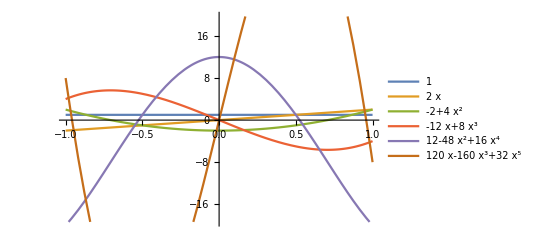

```mathematica
Plot[Evaluate[Table[HermiteH[α, x],{α,0,5}]],{x,-1,1},PlotLegends->"Expressions"]
```

```mathematica
ComplexPlot3D[HermiteH[1/2, z],{z,-2-2I,2+2I},PlotLegends->Automatic]
```

-Graphics3D-

Hermite Polynomials

```mathematica
Grid[Table[{α,HermiteH[α,x]},{α,0,5}],Frame->All]//FullSimplify
```

0 | 1
1 | 2 x
2 | -2+4 x^2
3 | 4 x (-3+2 x^2)
4 | 4 (3+4 x^2 (-3+x^2))
5 | 8 x (15+4 x^2 (-5+x^2))

Recurrence Relation

```mathematica
2x HermiteH[α,x]-2α HermiteH[α-1,x]//FullSimplify
2α HermiteH[α-1,x]//FullSimplify
```

-2 α HermiteH[-1+α,x]+2 x HermiteH[α,x]

2 α HermiteH[-1+α,x]

The two identities are not applied automatically by Mathematica' s simplify function . Let us check them manually:

```mathematica
FullSimplify[HermiteH[α+1,x]==2x HermiteH[α,x]-2α HermiteH[α-1,x]]
FullSimplify[D[HermiteH[α,x],x]==2α HermiteH[α-1,x]]
```

True

True

Orthogonality

```mathematica
ParallelTable[1/(Sqrt[π] 2^α α!)Integrate[Exp[-x^2] HermiteH[α,x]HermiteH[β,x],{x,-∞,∞}],{α,5},{β,5}]//FullSimplify//MatrixForm
```

(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)